```mathematica
(*Simulation Name*)
SimName = "L0009";
order = 8;
(*------------------------------------------------------------------------*)
<<SimulationTools`;
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

```mathematica
(*Old Way of Finding cm but produces the same result*)
h1 = 1. / (32 );
h2 = 1. / (36 );
h3 = 1. / (40 );
cm = ConvergenceMultiplier[{h1,h2,h3},order]
```

2.74924

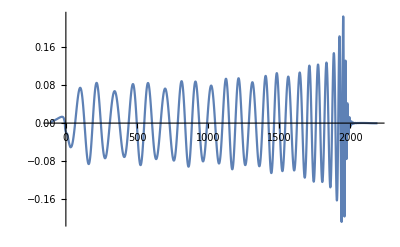

```mathematica
(*Import Strain Data*)
f1 = Import["C:\\Users\\eagle\\Box Sync\\Research_Backup\\Research\\Convergence\\Data_2_28_18\\"<>SimName<>"_N32\\"<>SimName<>"_N32_radially_extrapolated_strain_l2_m2.dat","Table"];
f2 = Import["C:\\Users\\eagle\\Box Sync\\Research_Backup\\Research\\Convergence\\Data_2_28_18\\"<>SimName<>"_N36\\"<>SimName<>"_N36_radially_extrapolated_strain_l2_m2.dat","Table"];
f3 = Import["C:\\Users\\eagle\\Box Sync\\Research_Backup\\Research\\Convergence\\Data_2_28_18\\"<>SimName<>"_N40\\"<>SimName<>"_N40_radially_extrapolated_strain_l2_m2.dat","Table"];

(*Get hplus and hcross from strain*)
hplus1 = Transpose[{f1[[All,1]],f1[[All,2]]}];
hcross1 = Transpose[{f1[[All,1]],f1[[All,3]]}];
hplus2 = Transpose[{f2[[All,1]],f2[[All,2]]}];
hcross2 = Transpose[{f2[[All,1]],f2[[All,3]]}];
hplus3 = Transpose[{f3[[All,1]],f3[[All,2]]}];
hcross3 = Transpose[{f3[[All,1]],f3[[All,3]]}];

ListLinePlot[hcross3]

(*Combine hplus and hcross into a complex number*)
complex1 = Transpose[{hplus1[[All,1]],hplus1[[All,2]]  + (hcross1[[All,2]] *ⅈ)}];
complex2 = Transpose[{hplus2[[All,1]],hplus2[[All,2]]  + (hcross2[[All,2]] *ⅈ)}];
complex3 =Transpose[{hplus3[[All,1]],hplus3[[All,2]]  + (hcross3[[All,2]] *ⅈ)}];

(*Define a function to extract the phase from a complex number*)
(*Gotten from https://mathematica.stackexchange.com/questions/5782/implementing-continuous-phase-arg-function/5784#5784*)
phase[vec_List]:=Module[{phi,df,len,i},
phi=Arg@vec;
df=Differences@phi;
len=Length@phi;
i=Flatten@Position[df,x_/;Abs[x]>3.5];
Do[phi=phi-(2Pi*Sign[df[[j]]]*UnitStep[#-(j+1)]&/@Range[len]),{j,i}];
phi]

(*Construct arrays of time and phase.*)
f1 = Transpose[{complex1[[All,1]],-phase[complex1[[All,2]]]}];
f2 = Transpose[{complex2[[All,1]],-phase[complex2[[All,2]]]}];
f3 = Transpose[{complex3[[All,1]],-phase[complex3[[All,2]]]}];
```

```mathematica
(*New way of defining Convergence Multiplier*)
deltat1 = Abs[f1[[2,1]] - f1[[1,1]]];
deltat2 = Abs[f2[[2,1]] - f2[[1,1]]];
deltat3 = Abs[f3[[2,1]] - f3[[1,1]]];
cm = ConvergenceMultiplier[{deltat1,deltat2,deltat3},order]
```

2.74924

```mathematica
(*The distance along the x-axis the x-values will be moved to have the data start at 0*)
moveValues = {f1[[All,1]][[1]],f2[[All,1]][[1]],f3[[All,1]][[1]]};
```

```mathematica
(*Move Lists*)
f1[[All,1]]  = f1[[All,1]] +Abs[moveValues[[1]]];
f2[[All,1]] = f2[[All,1]] + Abs[moveValues[[2]]];
f3[[All,1]] = f3[[All,1]] + Abs[moveValues[[3]]];

(*Find starting point and ending point for Interpolation*)
xvals1 = f1[[All,1]];
xvals2 = f2[[All,1]];
xvals3 = f3[[All,1]];
startxvals = {xvals1[[1]],xvals2[[1]],xvals3[[1]]};
endxvals = {Last[xvals1],Last[xvals2],Last[xvals3]};
startPoint = startxvals[[1]]
endPoint = Min[endxvals]
```

0.

2297.92581818205652

```mathematica
(*Turn into Interpolating Functions*)
f1int = Interpolation[f1];
f2int = Interpolation[f2];
f3int = Interpolation[f3];

(*Interpolate from startPoint to endPoint using deltat time steps*)
f1intlim=Table[{t,f1int[t]},{t,startPoint,endPoint,deltat1}];
f2intlim=Table[{t,f2int[t]},{t,startPoint,endPoint,deltat2}];
f3intlim=Table[{t,f3int[t]},{t,startPoint,endPoint,deltat3 }];
```

```mathematica
(*Find the amplitude of the highest resolution*)
amp = Transpose[{hplus3[[All,1]],Sqrt[hplus3[[All,2]]^2 + hcross3[[All,2]]^2]}];
(*Use this to find the time of merger*)
merger = Max[amp[[All,2]]];
mergerTime = 0;
Do[
If[amp[[i,2]] == merger,
mergerTime = amp[[i,1]];
]
,{i,1,Length[amp]}]
mergerTime;
```

```mathematica
(*Create List of Lists*)
fsintlim = {f1intlim,f2intlim,f3intlim};
```

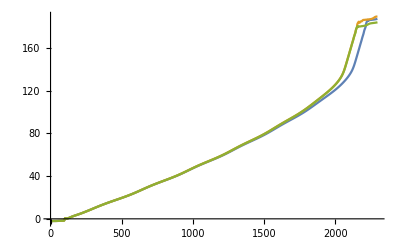

-Graphics-

{0,0}

```mathematica
(*Find indices where this is most likely a shift of N*pi. I used 650 because all of the cases I had showed a shift by this value*)
(*May be better to change to be after one cycle*) 
index = {0,0};
index40 = {0,0};
piInt = {0,0};(*32 - 40, 36 - 40*)
differences = {0,0};
diffval = 650;
differences[[1]] = (f1int[diffval]-f3int[diffval]);
differences[[2]] = (f2int[diffval]-f3int[diffval]);

(*Find if there is a difference of N*pi between the highest resolution phase data and the others. Move others to match highest resolution*)

ListLinePlot[{f1intlim,f2intlim,f3intlim}]

Do[
piInt[[i]] = Round[(differences[[i]]) / Pi];
fsintlim[[i]][[All,2]] = fsintlim[[i]][[All,2]] - (Pi * piInt[[i]]);
,{i,1,2}]


f1intlim = fsintlim[[1]];
f2intlim = fsintlim[[2]];
ListLinePlot[{f1intlim,f2intlim,f3intlim}]
piInt
```

```mathematica
(*Turn into Data Tables*)
f1intlimdat = ToDataTable[f1intlim];
f2intlimdat = ToDataTable[f2intlim];
f3intlimdat = ToDataTable[f3intlim];
```

```mathematica
plotPoint = 150;

(*Resample the Data Tables and turn them into lists*)
resampledDataTables = ResampleDataTables[{f1intlimdat,f2intlimdat,f3intlimdat}];
f1list = ToList[resampledDataTables[[1]]];
f2list = ToList[resampledDataTables[[2]]];
f3list = ToList[resampledDataTables[[3]]];


xvalsExport = f1list[[All,1]];

(*Prepare Merger Line Data for export*)
ylist = Array[#&,Length[f1list[[All,1]]],{0,Max[f1list[[All,2]]]}];
xlist = Table[mergerTime,{i,1,Length[ylist]}];
mergerLine = Transpose[{xlist,ylist}];

(*Export data*)
exportData=Flatten/@Transpose[{xvalsExport,f1list[[All,2]],f2list[[All,2]],f3list[[All,2]],mergerLine[[All,1]],mergerLine[[All,2]]}];
(*exportData=Flatten/@Transpose[{xvalsExport,f1list[[All,2]],f2list[[All,2]],f3list[[All,2]],mergerLine[[All,1]],mergerLine[[All,2]],plotPoint,endPoint}]*)
exportData//MatrixForm;
(*Export["C:\\Users\\eagle\\Desktop\\Research\\Convergence\\Test\\exportDataCombined_"<>ToString[SimName]<>".dat",exportData,"Table"];*)
```

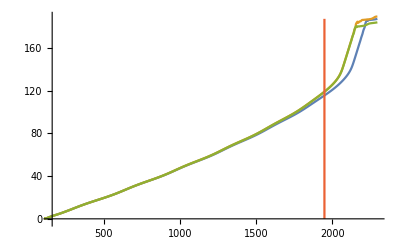

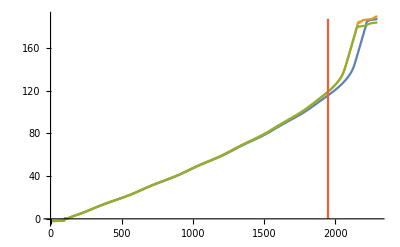

```mathematica
(*Examine the plots if needed*)
ListLinePlot[{f1list,f2list , f3list,mergerLine},PlotRange->{{plotPoint,endPoint},All}]
ListLinePlot[{f1list,f2list , f3list,mergerLine},PlotRange->All]
(*Export["C:\\Users\\eagle\\OneDrive\\Documents\\College\\Research\\SPIN-Derek\\"<>SimName<>"\\phase_data_tables.png",ListLinePlot[{f1,f2,f3}]];*)
```

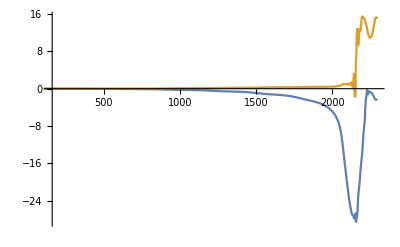

```mathematica
ListLinePlot[{f1intlimdat - f2intlimdat, (f2intlimdat - f3intlimdat) cm}, PlotRange->{{plotPoint,endPoint},All}]//WithResampling
(*Export["C:\\Users\\eagle\\OneDrive\\Documents\\College\\Research\\SPIN-Derek\\"<>SimName<>"\\ratio_between_differences.png",WithResampling[ListLinePlot[{f1 - f2, (f2 - f3) cm}]]];*)
```

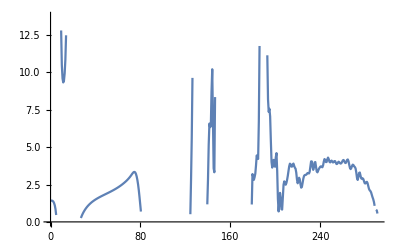

```mathematica
ListLinePlot[ConvergenceRate[{f1intlimdat,f2intlimdat,f3intlimdat},{deltat1,deltat2,deltat3}],PlotRange->All]
(*Export["C:\\Users\\eagle\\OneDrive\\Documents\\College\\Research\\SPIN-Derek\\"<>SimName<>"\\convergence_rate.png",ListLinePlot[ConvergenceRate[{f1,f2,f3},{h1,h2,h3}],PlotRange->All]];*)
```

```mathematica
(*************************************************************************************)
(*Phase Error Plots*)
fExt = RichardsonExtrapolant[{f2intlimdat,f3intlimdat},{deltat2,deltat3},order]
```

DataTable[<3657>,{{0.,2297.29745454569}}]

```mathematica
fErr = WithResampling[f3intlimdat - fExt];
```

```mathematica
fErrList = ToList[fErr];
ylistErr = Array[#&,Length[fErrList[[All,1]]],{0,Max[fErrList[[All,2]]]}];
xlistErr = Table[mergerTime,{i,1,Length[ylistErr]}];
mergerLineErr = Transpose[{xlistErr,ylistErr}];
mergerLineErrDat = ToDataTable[mergerLineErr];

(*Export Data. I then take it into Python and use Matplotlib to make the plots.*)
exportDataErr=Flatten/@Transpose[{fErrList[[All,1]],fErrList[[All,2]],mergerLineErr[[All,1]],mergerLineErr[[All,2]]}]
(*Export["C:\\Users\\eagle\\Desktop\\Research\\Convergence\\Test\\exportDataCombined_"<>ToString[SimName]<>".dat",exportDataErr,"Table"];*)
```

{{0.,-0.00255945,1949.51111981741633,0.},{0.6283636363637,-0.00227401,1949.51111981741633,0.00116401},{1.2567272727274,-0.00199884,1949.51111981741633,0.00232802},3652,{2296.66909090933,4.15751,1949.51111981741633,4.25446},{2297.29745454569,4.14891,1949.51111981741633,4.25562}}
 |  |  |  |

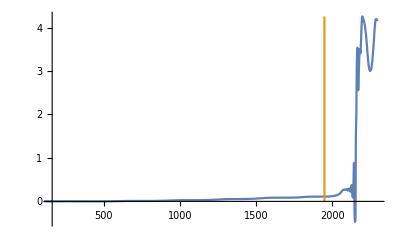

```mathematica
ListLinePlot[{fErr,mergerLineErrDat},PlotRange->{{plotPoint,endPoint},All}]
(*Export["C:\\Users\\eagle\\OneDrive\\Documents\\College\\Research\\SPIN-Derek\\"<>SimName<>"\\N40_error.png",ListLinePlot[fErr,PlotRange->All]];*)
```

```mathematica
(*****************************************************************************************)
(*The rest of this was used for error diagnosis purposes. Will leave in just in case*)
```

```mathematica
(*strain = Import["C:\\Users\\eagle\\Desktop\\Research\\Convergence\\Data\\"<>SimName<>"_N32_LIGO_Data\\strain.dat","Table"]*)
```

```mathematica
(*time = strain[[All,1]];
hplus = strain[[All,2]];
hcross = strain[[All,3]];*)
```

```mathematica
(*angle = ArcTan[hcross / hplus];
Transpose[{time,hplus}]*)
```

```mathematica
(*ListLinePlot[Transpose[{time,hplus}],PlotRange->All]*)
```

```mathematica
(*amp = Sqrt[hplus^2 + hcross^2];
ListPlot[Transpose[{time,amp}]]*)
```

```mathematica
(*psi4 = Import["C:\\Users\\eagle\\Desktop\\Research\\Convergence\\Data\\Psi4\\"<>SimName<>"_N32_psi4.dat","Table"]
psi4[[All,2]];
psi4//.{I -> 2}
ListLinePlot[Re[psi4], PlotRange->All]*)
```